## Prove that the family r(x_0)=u/x_R [δ(x_0-x_R)+δ(x_0+x_R)] is the optimal resetting strategy for the sixth order polynomial distribution

```mathematica
pbc[a_,xT_]:= a xT^2+(4-3 a) xT^4+7/30 (-9+8 a) xT^6;;
```

```mathematica
Manipulate[Plot[pbc[a,x],{x,0,1}],{{a,1},0,1/23 (117+√8169)}]
```

### Solution of the MFPT for r(x_0)=u/x_R [δ(x_0-x_R)+δ(x_0+x_R)]+ϵ [δ(x_0-x)+δ(x_0+x)]

#### 11 : 0<x_T<x_R , -1<x<-x_R

```mathematica
sol11=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F3''[x0]==-1,F1[-1]==0,F1[x]==F2[x],F2'[x]-F1'[x]==ϵ*F1[x],F2[-xR]==F3[-xR],F3'[-xR]-F2'[-xR]==ux/xR F2[-xR],F3[0]==0},{F1[x0],F2[x0],F3[x0]},x0];
M11=FullSimplify[Limit[D[-F3[x0]/.sol11[[1]]/.x0->xT,ϵ],ϵ->0]];
M11m=FullSimplify[Limit[D[-F3[x0]/.sol11[[1]]/.x0->xT,ϵ],ϵ->0]]/.x->-x;
```

#### 12 : 0<x_T<x_R , -x_R<x<0

```mathematica
sol12=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F3''[x0]==-1,F1[-1]==0,F2[x]==F3[x],F3'[x]-F2'[x]==ϵ*F2[x],F1[-xR]==F2[-xR],F2'[-xR]-F1'[-xR]==ux/xR F1[-xR],F3[0]==0},{F1[x0],F2[x0],F3[x0]},x0];
M12=FullSimplify[Limit[D[-F3[x0]/.sol12[[1]]/.x0->xT,ϵ],ϵ->0]];
M12m=FullSimplify[Limit[D[-F3[x0]/.sol12[[1]]/.x0->xT,ϵ],ϵ->0]]/.x->-x;
```

#### 13 : 0<x_T<x_R , 0<x<x_T

```mathematica
sol13=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F3''[x0]==-1,F1[-1]==0,F2[x]==F3[x],F3'[x]-F2'[x]==ϵ*F2[x],F1[-xR]==F2[-xR],F2'[-xR]-F1'[-xR]==ux/xR F1[-xR],F2[0]==0},{F1[x0],F2[x0],F3[x0]},x0];
M13=FullSimplify[Limit[D[-F3[x0]/.sol13[[1]]/.x0->xT,ϵ],ϵ->0]];
M13m=FullSimplify[Limit[D[-F3[x0]/.sol13[[1]]/.x0->xT,ϵ],ϵ->0]]/.x->-x;
```

```mathematica
M1=Piecewise[{{M11,-1<=x<-xR},{M12,-xR<=x<0},{M13,0<=x<xT}}]
```

Piecewise[{{-((1+x)^2 (x (-1+ux (-1+xR))+ux (-1+xR) xR) xT)/(2 (1+ux-ux xR)^2), -1≤x<-xR}, {(x ((1+x)^2 xR+ux^2 (-1+xR)^2 (x+xR)^2-ux (1+x) (x+xR) (-1+xR^2)) xT)/(2 (-1+ux (-1+xR))^2 xR), -xR≤x<0}, {-(x (-1+x (-1+ux (-1+xR))+ux (-1+xR) xR) (x-xT))/(-2+2 ux (-1+xR)), 0≤x<xT}, {0, True}}]

#### 21 : x_R<x_T<1 , -1<x<-x_R

```mathematica
sol21=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F3''[x0]==-1,F4''[x0]==-1,F1[-1]==0,F1[x]==F2[x],F2'[x]-F1'[x]==ϵ*F1[x],F2[-xR]==F3[-xR],F3'[-xR]-F2'[-xR]==ux/xR F2[-xR],F3[0]==0,F3[xR]==F4[xR],F4'[xR]-F3'[xR]==ux/xR F3[xR]},{F1[x0],F2[x0],F3[x0],F4[x0]},x0];
M21=FullSimplify[Limit[D[-F4[x0]/.sol21[[1]]/.x0->xT,ϵ],ϵ->0]];
M21m=FullSimplify[Limit[D[-F4[x0]/.sol21[[1]]/.x0->xT,ϵ],ϵ->0]]/.x->-x;
```

#### 22 : x_R<x_T<1 , -x_R<x<0

```mathematica
sol22=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F3''[x0]==-1,F4''[x0]==-1,F1[-1]==0,F2[x]==F3[x],F3'[x]-F2'[x]==ϵ*F2[x],F1[-xR]==F2[-xR],F2'[-xR]-F1'[-xR]==ux/xR F1[-xR],F3[0]==0,F3[xR]==F4[xR],F4'[xR]-F3'[xR]==ux/xR F3[xR]},{F1[x0],F2[x0],F3[x0],F4[x0]},x0];
M22=FullSimplify[Limit[D[-F4[x0]/.sol22[[1]]/.x0->xT,ϵ],ϵ->0]];
M22m=FullSimplify[Limit[D[-F4[x0]/.sol22[[1]]/.x0->xT,ϵ],ϵ->0]]/.x->-x;
```

#### 23 : x_R<x_T<1 , 0<x<x_R

```mathematica
sol23=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F3''[x0]==-1,F4''[x0]==-1,F1[-1]==0,F2[x]==F3[x],F3'[x]-F2'[x]==ϵ*F2[x],F1[-xR]==F2[-xR],F2'[-xR]-F1'[-xR]==ux/xR F1[-xR],F2[0]==0,F3[xR]==F4[xR],F4'[xR]-F3'[xR]==ux/xR F3[xR]},{F1[x0],F2[x0],F3[x0],F4[x0]},x0];
M23=FullSimplify[Limit[D[-F4[x0]/.sol23[[1]]/.x0->xT,ϵ],ϵ->0]];
M23m=FullSimplify[Limit[D[-F4[x0]/.sol23[[1]]/.x0->xT,ϵ],ϵ->0]]/.x->-x;
```

### 24 : x_R<x_T<1 , x_R<x<x_T

```mathematica
sol24=DSolve[{F1''[x0]==-1,F2''[x0]==-1,F3''[x0]==-1,F4''[x0]==-1,F1[-1]==0,F3[x]==F4[x],F4'[x]-F3'[x]==ϵ*F3[x],F1[-xR]==F2[-xR],F2'[-xR]-F1'[-xR]==ux/xR F1[-xR],F2[0]==0,F2[xR]==F3[xR],F3'[xR]-F2'[xR]==ux/xR F2[xR]},{F1[x0],F2[x0],F3[x0],F4[x0]},x0];
M24=FullSimplify[Limit[D[-F4[x0]/.sol24[[1]]/.x0->xT,ϵ],ϵ->0]];
M24m=FullSimplify[Limit[D[-F4[x0]/.sol24[[1]]/.x0->xT,ϵ],ϵ->0]]/.x->-x;
```

```mathematica
M2=Piecewise[{{M21,-1<=x<-xR},{M22,-xR<=x<0},{M23,0<=x<xR},{M24,xR<=x<xT}}]
```

Piecewise[{{((1+x)^2 (x (-1+ux (-1+xR))+ux (-1+xR) xR) (ux xR-(1+ux) xT))/(2 (1+ux-ux xR)^2), -1≤x<-xR}, {-(x ((1+x)^2 xR+ux^2 (-1+xR)^2 (x+xR)^2-ux (1+x) (x+xR) (-1+xR^2)) (ux xR-(1+ux) xT))/(2 (-1+ux (-1+xR))^2 xR), -xR≤x<0}, {(x (-1+x (-1+ux (-1+xR))+ux (-1+xR) xR) ((-1+ux) x xR-ux x xT+xR (xT+ux (-xR+xT))))/(2 (-1+ux (-1+xR)) xR), 0≤x<xR}, {(((1+ux) x (1+x)+ux (-1+(2+2 ux-x) x) xR-ux (1+2 ux) (1+x) xR^2+2 ux^2 xR^3) (x-xT))/(-2+2 ux (-1+xR)), xR≤x<xT}, {0, True}}]

```mathematica
Mp=Piecewise[{{M1,0<xT<=xR},{M2,xR<xT<=1}}];
Mm=Mp/.{x->-x,xT->-xT};
M=Mp+Mm;
Mt=Piecewise[{{-1/2 Abs[x*xT](1-Abs[x])^2,x*xT<0},{1/2 Abs[x](Abs[xT]-Abs[x])(1+Abs[x]),x*xT>0&&Abs[xT]>Abs[x]}}]
```

Piecewise[{{-1/2 (1-Abs[x])^2 Abs[x xT], x xT<0}, {1/2 Abs[x] (1+Abs[x]) (-Abs[x]+Abs[xT]), x xT>0&&Abs[xT]>Abs[x]}, {0, True}}]

## Functional derivative μ(x)

```mathematica
I1c1=Integrate[pbc[a,xT]M24m,{xT,-x,1}];
I2c1=Integrate[pbc[a,xT]M11,{xT,0,xR}]+Integrate[pbc[a,xT]M21,{xT,xR,1}];
I1c2=Integrate[pbc[a,xT]M13m,{xT,-x,xR}]+Integrate[pbc[a,xT]M23m,{xT,xR,1}];
I2c2=Integrate[pbc[a,xT]M12,{xT,0,xR}]+Integrate[pbc[a,xT]M22,{xT,xR,1}];
I1c3=Integrate[pbc[a,xT]M12m,{xT,0,xR}]+Integrate[pbc[a,xT]M22m,{xT,xR,1}];
I2c3=Integrate[pbc[a,xT]M13,{xT,x,xR}]+Integrate[pbc[a,xT]M23,{xT,xR,1}];
I1c4=Integrate[pbc[a,xT]M11m,{xT,0,xR}]+Integrate[pbc[a,xT]M21m,{xT,xR,1}];
I2c4=Integrate[pbc[a,xT]M24,{xT,x,1}];
```

```mathematica
mu=Piecewise[{{I1c1+I2c1,-1<=x<-xR},{I1c2+I2c2,-xR<=x<0},{I1c3+I2c3,0<=x<xR},{I1c4+I2c4,xR<=x<1}}];
```

```mathematica
Integrate[pbc[a,xT]Mt,{xT,-1,1},Assumptions->{-1<x<1}]
```

Piecewise[{{1/480 (171 x^2-12 a x^2+217 x^3-4 a x^3-20 a x^5+20 a x^6-32 x^7+24 a x^7+32 x^8-24 a x^8+9 x^9-8 a x^9-9 x^10+8 a x^10), -1<x<0}, {1/480 (171 x^2-12 a x^2-217 x^3+4 a x^3+20 a x^5+20 a x^6+32 x^7-24 a x^7+32 x^8-24 a x^8-9 x^9+8 a x^9-9 x^10+8 a x^10), 0<x<1}, {0, True}}]

For u->0 we get the perturbation with respect the no-resetting

```mathematica
Manipulate[Show[Plot[{mu/.{xR->0.1,a->av,ux->0}},{x,0,1}],Plot[1/480 (171 x^2-12 a x^2-217 x^3+4 a x^3+20 a x^5+20 a x^6+32 x^7-24 a x^7+32 x^8-24 a x^8-9 x^9+8 a x^9-9 x^10+8 a x^10)/.a->av,{x,0,1},PlotStyle->{Dashed,Red}]],{{av,9},0,1/23 (117+√8169)}]
```

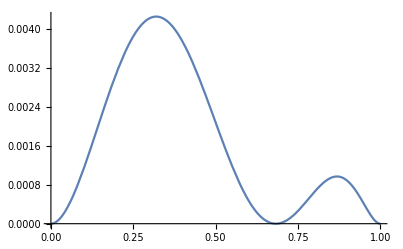

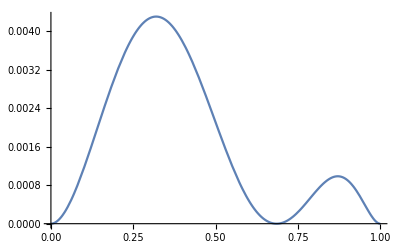

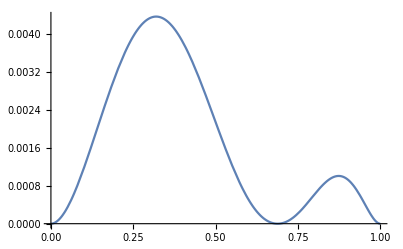

```mathematica
Plot[{mu/.{xR->0.6828564981636954,ux->0.21964087889349027,a->8.5}},{x,0,1}]
Plot[{mu/.{xR->0.6852322374356223,ux->0.47277014047337207,a->8.75}},{x,0,1}]
Plot[{mu/.{xR->0.6882644406973737,ux->0.7961692940403322,a->9}},{x,0,1}]
```